```mathematica
Remove["Global`*"];
SetAttributes[{k,m,b}, Constant]
$Assumptions={Element[{k,m,b}, Reals]&&b≥0 &&k>0 &&m>0};
(*solving with fixed ends*)
x[0][t]=0;
x[4][t]=0;

T=1/2m Sum[x[i]'[t]^2, {i,1,3}];
V=Sum[1/2 k (x[i][t]-x[i-1][t])^2 + b (x[i][t]-x[i-1][t])^4 ,{i,1,4}];
lag=T-V;

EL[q_]:=D[lag,q]-Dt[D[lag, D[q,t]],t];

(*NL for non-linear*)
NLeqnarray=Table[EL[x[i][t]], {i,1,3}]//Simplify;
Print["The equations of motion are:"]
Print["for the first mass:\n"NLeqnarray[[1]]==0]
Print["second mass:\n"NLeqnarray[[2]]==0]
Print["third mass:\n"NLeqnarray[[3]]==0]

(*for linear approx, we solve the usual way and set b=0*)
x[i_][t_]:=A[i] E^(I ω t);

eqnarray=NLeqnarray/E^(I ω t)//Simplify;

(*for b=0*)

b=0;
eqnarray//MatrixForm
x[i_][t_]:=A[i] E^(I ω t);
matrix=Table[ D[eqnarray[[i]],A[j]]//Simplify, {i,1,3}, {j, 1, 3}];
soln=Solve[Det[matrix/.ω^2->α]==0,α]//Simplify;
Ω=√(α/.soln)//Simplify; 
Print["The eigenfrequencies are:"]
Print[" ",Ω[[1]]]
Print[" ",Ω[[2]]]
Print[" ",Ω[[3]]]

alist=Table[a[i], {i,1,3}];

eigena=Table[alist/.Solve[matrix.alist==0/.ω->Ω[[i]], alist][[1]]//Quiet//Simplify, {i,1,3}];
nrule=Table[a[i]->1 ,{i,1,3}];
eigena=eigena/.nrule;
Print["The Eigenmodes corresponding to each eigenfrequency are: ", eigena]
```

The equations of motion are:

for the first mass:
 (-k x[1][t]-4 b (x[1][t])^3+k (-x[1][t]+x[2][t])+4 b (-x[1][t]+x[2][t])^3-m x[1]''[t])==0

second mass:
 (k (x[1][t]-x[2][t])+4 b (x[1][t]-x[2][t])^3+k (-x[2][t]+x[3][t])+4 b (-x[2][t]+x[3][t])^3-m x[2]''[t])==0

third mass:
 (k (x[2][t]-x[3][t])+4 b (x[2][t]-x[3][t])^3-k x[3][t]-4 b (x[3][t])^3-m x[3]''[t])==0

(m ω^2 A[1]+k (-2 A[1]+A[2])
k (A[1]-A[2])+m ω^2 A[2]+k (-A[2]+A[3])
k (A[2]-2 A[3])+m ω^2 A[3])

The eigenfrequencies are:

√2 √(k/m)

√(-((-2+√2) k)/m)

√(2+√2) √(k/m)

The Eigenmodes corresponding to each eigenfrequency are: {{1,0,-1},{1,√2,1},{1,-√2,1}}

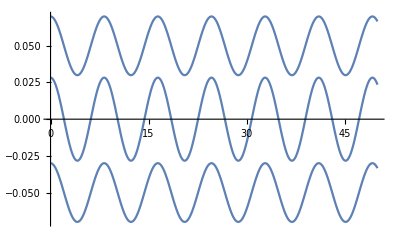

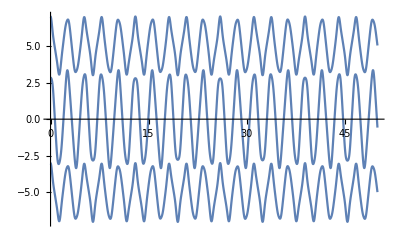

```mathematica
Remove["Global`*"];
SetAttributes[{k,m,b}, Constant]
$Assumptions={Element[{k,m,b}, Reals]&&b≥0 &&k>0 &&m>0};
(*solving with fixed ends*)
x[0][t]=0;
x[4][t]=0;

T=1/2m Sum[x[i]'[t]^2, {i,1,3}];
V=Sum[1/2 k (x[i][t]-x[i-1][t])^2 + b (x[i][t]-x[i-1][t])^4 ,{i,1,4}];
lag=T-V;

EL[q_]:=D[lag,q]-Dt[D[lag, D[q,t]],t];

(*NL for non-linear*)
NLeqnarray=Table[EL[x[i][t]]==0, {i,1,3}]//Simplify;

(*Physical Parameters*)
b=1;
m=1;
k=1;

tlo=0;
thi=50;


(*For the first mode the displacements are related by the eigenmode found in part 1*)
(*small displacements*)
x10=x[1][0]==.02;
x20=x[2][0]==.02 2^(1/2);
x30=x[3][0]==.02;
v10=x[1]'[0]==0;
v20=x[2]'[0]==0;
v30=x[3]'[0]==0;




iclist={x10,x20,x30,v10,v20,v30};
qlist=Table[x[i][t],{i,1,3}];

soln=NDSolve[{NLeqnarray,iclist}, qlist,{t,tlo,thi}];

Plot[{x[1][t]+.05,x[2][t],x[3][t]-.05}/.soln,{t,tlo,thi}]

(*Larger displacements*)
x11=x[1][0]==2;
x21=x[2][0]==2 2^(1/2);
x31=x[3][0]==2;
v11=x[1]'[0]==0;
v21=x[2]'[0]==0;
v31=x[3]'[0]==0;




iclist={x11,x21,x31,v11,v21,v31};

soln=NDSolve[{NLeqnarray,iclist}, qlist,{t,tlo,thi}];

Plot[{x[1][t]+5,x[2][t],x[3][t]-5}/.soln,{t,tlo,thi}]
```

```mathematica
The above plot shows diplacement as a function of time for each mass. The masses are in phase with appropriate amplitudes for the first mode.This essentially looks exactly like the non linear case
```

-Graphics-

```mathematica
This plot is for larger displacements. You can see as the displacement amplitude is larger, the non-linear behavior is apparent. The graph shows some variation in amplitudes, most evidently seen on the middle mass. All of the masses have a more jagged displacement vs time graph. This is due to the oscellation being a superposition of more than one frequency.

The coupling does not seem weak since the masses seem to stay in phase.
```